## Import and processing

```mathematica
(*SetDirectory[$InitialDirectory];*)
rawdata = Import["/data1/user_data/github/github-research/extendedcontributorsnew.txt"];
data$lines = StringSplit[rawdata,"\n"];
data$noheader= data$lines[[6;;Length@data$lines]];
array$string = StringSplit/@data$noheader;
Dimensions[array$string]
array = ToExpression/@array$string;
tarray = Transpose[array];
```

{33630,675}

## Array Generation

```mathematica
peopleList = StringSplit[data$lines[[5]]];
repoList = StringSplit[data$lines[[3]]];
(*repolist=Partition[repoList$doubled,2];*)
sparse$array=SparseArray@array;
sparse$tarray=SparseArray@tarray;
projectarray=SparseArray[sparse$array.sparse$tarray];
peoplearray=SparseArray[sparse$tarray.sparse$array];
noself$sparse$projectarray = UpperTriangularize[projectarray,1];
noself$sparse$peoplearray = UpperTriangularize[peoplearray,1];
```

## People Visualization (w/ export test)

```mathematica
peoplevis = AdjacencyGraph[noself$sparse$peoplearray,DirectedEdges->False];
(*Export["/data1/user_data/github/github-research/peoplevis.gml",peoplevis];
Import["/data1/user_data/github/github-research/peoplevis.gml"]*)
```

## Project visualization

```mathematica
projectvis=AdjacencyGraph[noself$sparse$projectarray,DirectedEdges->False];
```

## Functions

#### EgoGraph

```mathematica
egoGraph[node_,graph_]:=Module[{links,nodes,other,result},

links = EdgeList[graph, node<->_];
nodes = VertexList[links];
result=VertexDelete[graph,_?(!MemberQ[nodes,#]&)]
]
```

#### Centrality

```mathematica
centralityGraph[graph_,names_,threshold_]:=Module[{peopleCentrality,bigPos,biggestPos,labels,labels2,vertices},
peopleCentrality = Rescale[BetweennessCentrality[graph]];
vertices = VertexList[graph];
bigPos = Flatten[Position[peopleCentrality, _?(#>threshold&)]];
TableForm[labels = Table[vertices[[i]] -> names[[vertices[[i]]]]<> " "<>ToString[ peopleCentrality[[i]]], {i, bigPos}]]
]
```

#### Metrics

```mathematica
metrics[egograph_,names_, graphName_]:={graphName,centralityGraph[egograph,names,0.1],VertexCount[egograph],EdgeCount[egograph],N@Mean[VertexDegree[egograph]],N@GlobalClusteringCoefficient[egograph],N@MeanClusteringCoefficient[egograph],N@GraphAssortativity[egograph]}
```

## Testing

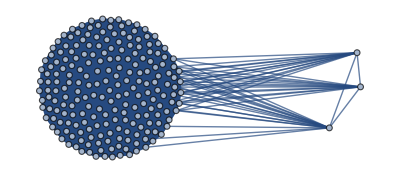

20→jlowin 0.272817
60→AlOa 1.
89→yosinski 1.
100→kashif 1.
115→MartinThoma 1.
126→benmccann 0.272817
135→hojonathanho 1.
137→viirya 1.
172→huyng 1.
177→jfsantos 1.
189→pra85 1.
195→shaibagon 1.
197→vikkamath 1.
200→xternalz 1.
201→yaroslavvb 0.272817
202→frankyjuang 0.272817
206→eulerreich 1.
288→eerwitt 0.0136609

```mathematica
randoGraph=egoGraph[200,peoplevis]
centralityGraph[randoGraph,peopleList,0.01]
```

```mathematica
gitterGraph=egoGraph[608,peoplevis];
centralityGraph[gitterGraph,peopleList,0.1]
```

189→pra85 0.19062
370→Lewuathe 0.115179
608→gitter-badger 1.
636→JoostvDoorn 0.267065

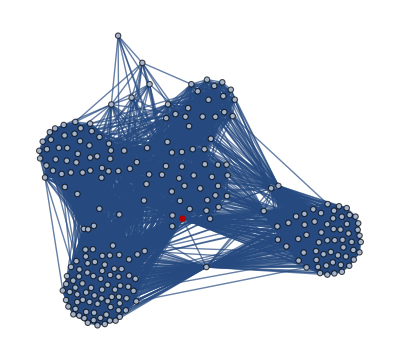

```mathematica
HighlightGraph[gitterGraph,608]
```

```mathematica
peopleList[[43]]
```

manzagop

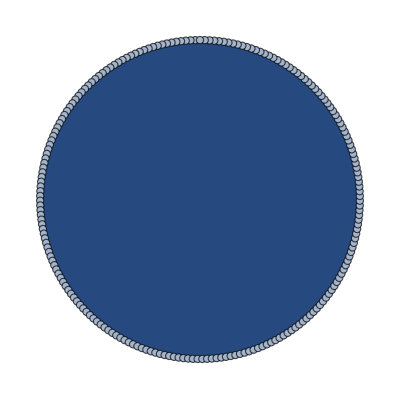

{}

```mathematica
circleGraph=egoGraph[43,peoplevis]
centralityGraph[circleGraph,peopleList,0.01]
```

```mathematica
metrics[gitterGraph,peopleList,"gitterBadger"]
```

Name | gitterBadger
Centrality | 189→pra85 0.19062
370→Lewuathe 0.115179
608→gitter-badger 1.
636→JoostvDoorn 0.267065
Number of Verticies | 244
Number of Edges | 7928
Mean Vertex Degree | 3964/61

## Testing 2:

```mathematica
ego$gitter=egoGraph[608,peoplevis];Export["/data1/user_data/github/github-research/gitterEgo.gml",ego$gitter];
metrics[ego$gitter,peopleList,"gitterbadger"]
```

Name | gitterbadger
Centrality | 189→pra85 0.19062
370→Lewuathe 0.115179
608→gitter-badger 1.
636→JoostvDoorn 0.267065
Number of Verticies | 244
Number of Edges | 7928
Mean Vertex Degree | 64.9836
GlobalClusteringCoefficient | 0.816958
MeanClusteringCoefficient | 0.873303
GraphAssociativity | 0.127461

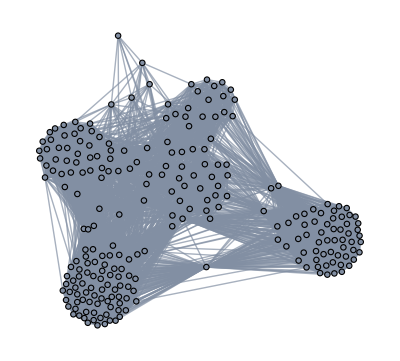

```mathematica
Import["/data1/user_data/github/github-research/gitterEgo.gml"];
```

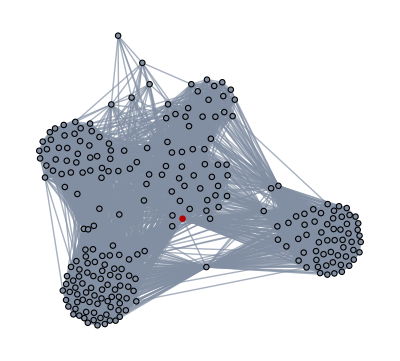

```mathematica
HighlightGraph[%,608];
```

```mathematica
repoList[[1;;6]]
```

{Theano:Theano,caffe:BVLC,CNTK:Microsoft,tensorflow:tensorflow,torch7:torch,deeplearning4j:deeplearning4j}

## COMPUTE:

```mathematica
{ego$theano,ego$caffe,ego$cntk,ego$tensorflow,ego$torch,ego$deeplearning4j}=egoGraph[#,projectvis]/@Range[6];
Export["/data1/user_data/github/github-research/egotheano.gml",ego$theano];
Export["/data1/user_data/github/github-research/egocaffe.gml",ego$caffe];
Export["/data1/user_data/github/github-research/egocntk.gml",ego$cntk];
Export["/data1/user_data/github/github-research/egotensorflow.gml",ego$tensorflow];
Export["/data1/user_data/github/github-research/egotorch.gml",ego$torch];
Export["/data1/user_data/github/github-research/egod4j.gml",ego$deeplearning4j];
```

Export::type: cannot be exported to the Graphlet format.

```mathematica
Grid[Transpose[Prepend[{"Name","Centrality","Number of Verticies","Number of Edges","Mean Vertex Degree", "GlobalClusteringCoefficient","MeanClusteringCoefficient","GraphAssociativity"},metrics/@}],Frame->All]
```

```mathematica
Export["/data1/user_data/github/github-research/egotheano.gxl",ego$theano];
Export["/data1/user_data/github/github-research/egocaffe.gxl",ego$caffe];
Export["/data1/user_data/github/github-research/egocntk.gxl",ego$cntk];
Export["/data1/user_data/github/github-research/egotensorflow.gxl",ego$tensorflow];
Export["/data1/user_data/github/github-research/egotorch.gxl",ego$torch];
Export["/data1/user_data/github/github-research/egod4j.gxl",ego$deeplearning4j];
```

Export::type: cannot be exported to the GXL format.

```mathematica
ego$2$tensorflow=egoGraph[1,projectvis];
```

```mathematica
Export["/data1/user_data/github/github-research/egotesttensor.gxl",ego$2$tensorflow]
```

/data1/user_data/github/github-research/egotesttensor.gxl

```mathematica
metrics[ego$2$tensorflow,repoList,"TensorTest"]
```

{TensorTest,1→Theano:Theano 1.
1067→changepoint:viveksck 1.
2024→hemi:harrism 0.336103
2029→AutoX:lucasb-eyer 1.
3638→box-plots-for-education:sergii-gavrylov 0.405807,4048,260248,128.581,0.674018,0.956234,-0.0656021}

```mathematica
ego$theano=ego$2$tensorflow;
ego$caffe=egoGraph[2,projectvis];
ego$cntk=egoGraph[3,projectvis];
ego$tensorflow=egoGraph[4,projectvis];
ego$d4j=egoGraph[6,projectvis];
```

```mathematica
Export["/data1/user_data/github/github-research/egoCaffe.gml",ego$caffe]
```

/data1/user_data/github/github-research/egoCaffe.gml

```mathematica
ego$torch=egoGraph[5,projectvis];
```

```mathematica
Grid[Transpose[{{"Name","Centrality","Number of Verticies","Number of Edges","Mean Vertex Degree", "GlobalClusteringCoefficient","MeanClusteringCoefficient","GraphAssociativity"},metrics[ego$theano,repoList,"Theano"],metrics[ego$caffe,repoList,"Caffe"],metrics[ego$cntk,repoList,"CNTK"],metrics[ego$tensorflow,repoList,"TensorFlow"],metrics[ego$torch,repoList,"Torch7"],metrics[ego$d4j,repoList,"Deeplearning4J"]}],Frame->All]
```

Name | Theano | Caffe | CNTK | TensorFlow | Torch7 | Deeplearning4J
Centrality | 1→Theano:Theano 1.
1067→changepoint:viveksck 1.
2024→hemi:harrism 0.336103
2029→AutoX:lucasb-eyer 1.
3638→box-plots-for-education:sergii-gavrylov 0.405807 | 2→caffe:BVLC 1.
1360→flann:mariusmuja 0.12122
5595→erlport:hdima 0.153566
5765→rbgirshick.github.io:rbgirshick 0.139989
5883→imsearch-tools:kencoken 0.263351
6100→bigdata-apriori:boechat107 0.282852
6147→cqstyle:crizCraig 0.132794
6382→itorch-docker:kkoba84 1.
6753→SPLTT-Release:jsupancic 0.169
7300→CVPR15-CFSS:zhusz 0.165343
7937→savage_jar_beasts:sjbrown 0.187247
8541→ba_thesis:panmari 0.215508
12232→resnet-1k-layers:KaimingHe 0.131662 | 3→CNTK:Microsoft 1.
4676→frontend:guardian 0.120179 | 4→tensorflow:tensorflow 1.
9353→leveldb:basho 0.935033
9763→keystone:concretevitamin 1. | 5→torch7:torch 1. | 6→deeplearning4j:deeplearning4j 1.
Number of Verticies | 4048 | 3120 | 421 | 2314 | 10080 | 9125
Number of Edges | 260248 | 240628 | 20681 | 68400 | 34441025 | 34252587
Mean Vertex Degree | 128.581 | 154.249 | 98.247 | 59.1184 | 6833.54 | 7507.42
GlobalClusteringCoefficient | 0.674018 | 0.660917 | 0.961794 | 0.350817 | 0.999238 | 0.999923
MeanClusteringCoefficient | 0.956234 | 0.96997 | 0.949221 | 0.956564 | 0.989846 | 0.9963
GraphAssociativity | -0.0656021 | -0.210453 | 0.644866 | -0.0727403 | 0.921698 | 0.919295